```mathematica
Clear[t];
Clear[X];
Clear[Y];
Clear[M];
Clear[Mt];
Clear[A];
Clear[Inv];
Clear[c];
Clear[B];
Clear[P];
Clear[σ1];
Clear[σ];
Clear[Eigs];
```

```mathematica
X=Table[RandomReal[{100,120}],{i,10^3}]; (*alpha_x*)
Y=Table[RandomReal[{100,120}],{i,10^3}]; (*alpha_y*)
t=1;(*time*)
(*Only able to take as constant at minute. If I allow time to be a variable then eigenvalues become functions of t at end and it is hard to see if they are positive or negative*)
```

```mathematica
M=Table[{{0,0,0,0,0,-Y[[i]]},{0,0,0,0,-Y[[i]],0},{0,0,0,0,0,X[[i]]},{0,0,0,0,-X[[i]],0},{0,-Y[[i]],0,X[[i]],0,0},{-Y[[i]],0,-X[[i]],0,0,0}},{i,1,Length[X]}];
MatrixForm[M[[1]]]
```

(0 | 0 | 0 | 0 | 0 | -112.099
0 | 0 | 0 | 0 | -112.099 | 0
0 | 0 | 0 | 0 | 0 | 107.652
0 | 0 | 0 | 0 | -107.652 | 0
0 | -112.099 | 0 | 107.652 | 0 | 0
-112.099 | 0 | -107.652 | 0 | 0 | 0)

```mathematica
Mt=Table[{{0,0,0,0,0,-Y[[i]]},{0,0,0,0,-Y[[i]],0},{0,0,0,0,0,X[[i]]},{0,0,0,0,-X[[i]],0},{0,-Y[[i]],0,X[[i]],0,0},{-Y[[i]],0,-X[[i]],0,0,0}}t,{i,1,Length[X]}];
MatrixForm[Mt[[1]]]
```

(0 | 0 | 0 | 0 | 0 | -4.8934
0 | 0 | 0 | 0 | -4.8934 | 0
0 | 0 | 0 | 0 | 0 | 7.13551
0 | 0 | 0 | 0 | -7.13551 | 0
0 | -4.8934 | 0 | 7.13551 | 0 | 0
-4.8934 | 0 | -7.13551 | 0 | 0 | 0)

```mathematica
σ0=IdentityMatrix[6];
(*initial covariance matrix representing initial state of experiment, x in coherent state, b and y in vacuum states.*)
MatrixForm[σ0]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
A=Table[MatrixExp[Mt[[i]]],{i,1,Length[Mt]}];
(*A defined as in notes; e^(Mt) exponential of the matrix*)
FullSimplify[MatrixForm[A[[1]]]]
```

(1.47715 | 0. | 0.695774 | 0. | 0. | 0.835384
0. | 1.47715 | 0. | -0.695774 | 0.835384 | 0.
-0.695774 | 0. | -0.0145728 | 0. | 0. | -1.21815
0. | 0.695774 | 0. | -0.0145728 | 1.21815 | 0.
0. | 0.835384 | 0. | -1.21815 | 0.462576 | 0.
0.835384 | 0. | 1.21815 | 0. | 0. | 0.462576)

```mathematica
Det[M[[1]]]//FullSimplify
(*Determinant equal to 0 so inverse of M doesn't exist*)
```

0.

```mathematica
Inv=Table[PseudoInverse[M[[i]]],{i,1,Length[M]}];
(*PseudoInverse of matrix M NOT including t. Using PseudoInverse as M is singular.*)
```

```mathematica
FullSimplify[MatrixForm[Inv[[1]]]]
(*The form of this matrix varies alot with different i*)
```

(0. | 0. | 0. | 0. | 0. | -0.0653665
0. | 0. | 0. | 0. | -0.0653665 | 0.
0. | 0. | 0. | 0. | 0. | -0.095317
0. | 0. | 0. | 0. | 0.095317 | 0.
0. | -0.0653665 | 0. | -0.095317 | 0. | 0.
-0.0653665 | 0. | 0.095317 | 0. | 0. | 0.)

```mathematica
c=Table[{{0},{0},{0},{0},{0},{-√2 X[[i]]*Y[[i]]}},{i,1,Length[X]}];
(*c as defined in notes*)
MatrixForm[c[[1]]]
```

(0
0
0
0
0
-49.38)

```mathematica
B=Table[A[[i]]-IdentityMatrix[6],{i,1,Length[A]}];
(*B as defined in notes*)
FullSimplify[MatrixForm[B[[1]]]]
```

(0.477149 | 0. | 0.695774 | 0. | 0. | 0.835384
0. | 0.477149 | 0. | -0.695774 | 0.835384 | 0.
-0.695774 | 0. | -1.01457 | 0. | 0. | -1.21815
0. | 0.695774 | 0. | -1.01457 | 1.21815 | 0.
0. | 0.835384 | 0. | -1.21815 | -0.537424 | 0.
0.835384 | 0. | 1.21815 | 0. | 0. | -0.537424)

```mathematica
P=Table[Inv[[i]].c[[i]],{i,1,Length[c]}];
(*P as defined in notes*)
FullSimplify[MatrixForm[P[[1]]]]
```

(3.2278
0.
4.70675
0.
0.
0.)

```mathematica
σ1=Table[A[[i]].σ0.Transpose[A[[i]]],{i,1,Length[A]}];
(*covariance matrix corresponding to the Homogenous solution of the vectorial differential eqn*)
FullSimplify[MatrixForm[Transpose[σ1[[1]]]]]
```

(3.36394 | 0. | -2.05552 | 0. | 0. | 2.46797
0. | 3.36394 | 0. | 2.05552 | 2.46797 | 0.
-2.05552 | 0. | 1.9682 | 0. | 0. | -1.16248
0. | 2.05552 | 0. | 1.9682 | 1.16248 | 0.
0. | 2.46797 | 0. | 1.16248 | 2.39573 | 0.
2.46797 | 0. | -1.16248 | 0. | 0. | 2.39573)

```mathematica
σ=Table[(A[[i]]).(σ0).(Transpose[A[[i]]])+(B[[i]].P[[i]]).(Transpose[B[[i]].P[[i]]]),{i,1,Length[A]}];
(*covariance matrix corresponding to the Non-Homogenous solution of the vectorial differential eqn, with all terms*)
FullSimplify[MatrixForm[Transpose[σ[[2]]]]]
```

(2.4606 | 0. | -6.05713 | 0. | 0. | 7.0358
0. | 1.18243 | 0. | 0.411676 | 0.478192 | 0.
-6.05713 | 0. | 26.0127 | 0. | 0. | -29.0541
0. | 0.411676 | 0. | 1.07766 | 0.0902022 | 0.
0. | 0.478192 | 0. | 0.0902022 | 1.10478 | 0.
7.0358 | 0. | -29.0541 | 0. | 0. | 34.7484)

```mathematica
Eigs=Table[Min[Eigenvalues[σ[[i]]]],{i,1,Length[σ]}];
(*Table of eigenvalues of the time evolved covariance matrix for each i. Should be 6 eigenvalues for each i*)
FullSimplify[Eigenvalues[σ[[1]]]]
Eigs[[1]]
```

{149.305,6.5758,1.,1.,0.968121,0.152073}

0.152073

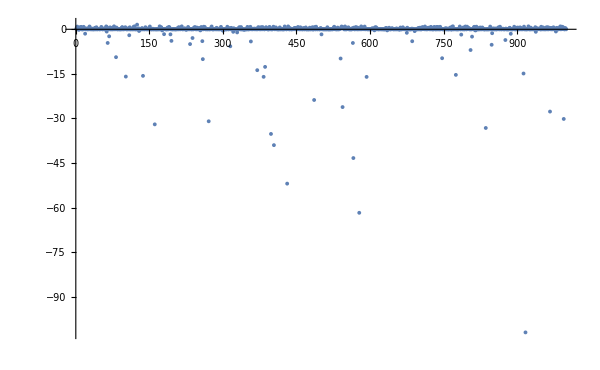

```mathematica
ListPlot[Table[{i,Eigs[[i]]},{i,1,Length[σ]}],PlotRange->All]
```